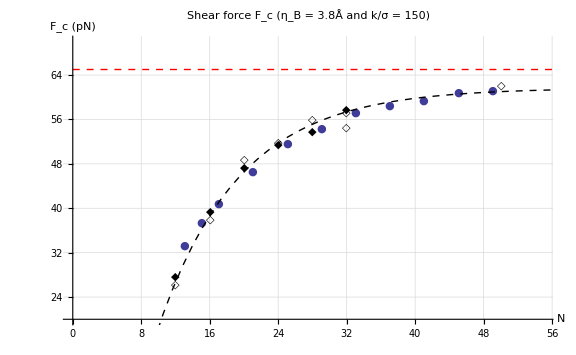

Parameters:
-------------------------------------
 η_B = 3.75	 κσr = 150.15

DeGennes Fit (Hatch Data):
-------------------------------------
 f_c = 3.23673 pN	 κσr = 181.462

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Subscript[η, B]=Last[Flatten[StringSplit[FileNames["ETA_B_*",NotebookDirectory[]],"_"]]];
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];

HatchData33Points=Import["./Hatch_Data/hatch33.dat","Table"];
HatchData55Points=Import["./Hatch_Data/hatch55.dat","Table"];

DataPoints=Transpose[Import["force.data","Table"]];
DataPointsFc=Table[{DataPoints[[1]][[i]],DataPoints[[2]][[i]]},{i,1,Length[DataPoints[[1]]]}];


AsymLevel=Table[{i,65},{i,0,60}];

fsTitle=24;
fsAxesLabel=16;
fs2=15;

Data=ListPlot[{HatchData33Points,HatchData55Points,DataPointsFc},PlotStyle->{{Black,FontSize->18},{Black,FontSize->18},{ColorData[1,1]}},PlotMarkers->{"◆","◇","●"}];
AsymLevelData =ListLinePlot[
{
AsymLevel
},
PlotStyle->{
{Thick,Dashed,Red}
}
];
legend={
{Graphics[{Black,Inset[Style["◆",FontSize->14],{0,0}]}],Style["3'3' Data",FontSize->fs2]},
{Graphics[{Black,Inset[Style["◇",FontSize->14],{0,0}]}],Style["5'5' Data",FontSize->fs2]},
{Graphics[{ColorData[1,1],Inset[Style["●",FontSize->14],{0,0}]}],Style["F_c",FontSize->fs2]}
};

DGmodel =2 Subscript[f, c] χ^-1 (1-2Exp[-χ  x]);

DeGennesfit = FindFit[HatchData55Points,DGmodel,{{Subscript[f, c],3.16},{χ,0.125}},x];
DeGennesFit=Plot[Evaluate[DGmodel /. DeGennesfit],{x,5,60},PlotStyle->{Thick,Dashed,Black}];

DeGennesκσr=(χ^2/2)^-1/.DeGennesfit;
Subscript[DeGennesf, c]=Subscript[f, c]/.DeGennesfit;


plot1=ShowLegend[Show[
{
Data,AsymLevelData,DeGennesFit
},
PlotRange->{{0,55},{20,70}},
PlotLabel->Style["Shear force F_c (η_B = 3.8Å and k/σ = 150)",FontSize->fsTitle],
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,20},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c (pN)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
ImageSize->Large
],{legend,LegendShadow->None,
LegendBorder->False,
LegendSize->{0.45,0.2},
LegendPosition->{0.2,-0.4},
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0]}]

Print["\nParameters:\n-------------------------------------\n η_B = ",Subscript[η, B] ,"\t κσr = ",κσr];
Print["\nDeGennes Fit (Hatch Data):\n-------------------------------------\n f_c = ",Subscript[DeGennesf, c] pN,"\t κσr = ",DeGennesκσr];
```